```mathematica
(*Part 1A*)
```

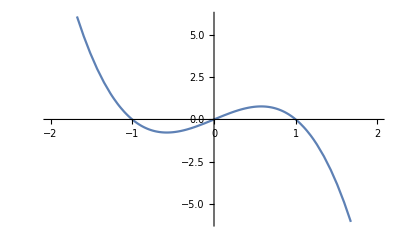

```mathematica
Plot[2y-2y^3,{y,-2,2}]
```

```mathematica
(*Steady States at y=-1, y=0, y=1
y=-1 is stable
y=0 is unstable
y=1 is stable*)

(*Evident from graph as well as fact that f'(y)=2-6y^2 so that
f'(1)=f'(-1)=-4 < 0 so those are stable
and f'(0)=2 > 0 so that one is unstable*)
```

```mathematica
Integrate[1/(1-y^2),y]
```

-1/2 Log[1-y]+1/2 Log[1+y]

```mathematica
Integrate[1/(2y-2y^3),y]
```

Log[y]/2-1/4 Log[1-y^2]

```mathematica
(*Initial Value 1 is y(0) = 1.5
Initial Value 2 is y(0) = 0.5*)
```

```mathematica
vv1 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==1.5},y,{t,0,20}]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
vv2 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==.5},y,{t,0,20}]
```

InterpolatingFunction[{{0., 20.}}, <>]

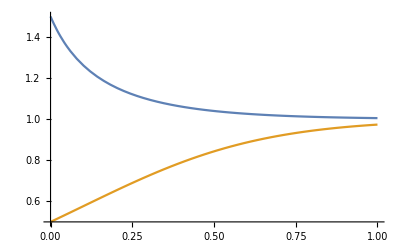

```mathematica
Plot[{vv1[t],vv2[t]},{t,0,1}]
```

```mathematica
(*Problem 1B*)
(*Steady state if e^(-y)=0 or sin(y)=0
First condition will never happen
sin(y)=0 if y=n*Pi for any integer n*)
(*It holds that f'(y)=e^(-y)(cos(y)-sin(y)) *)
(*Here is verification*)
D[Exp[-y]*Sin[y],y]
```

ⅇ^-y Cos[y]-ⅇ^-y Sin[y]

```mathematica
(*Steady states occur at n*Pi
e^(-y)>0 everywhere so we care about the sign of the other term
If y=2*n*Pi for integer n then cos(y)=1 so f'(y)>0 making those steady states unstable
If y=(2*n+1)*Pi for integer n then cos(y)=-1 so f'(y)<0 making those steady states stable *)
```

```mathematica
(*Here are two sample solutions*)
```

```mathematica
ww1 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==1},y,{t,0,20}];
```

```mathematica
ww2 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==2},y,{t,0,20}];
```

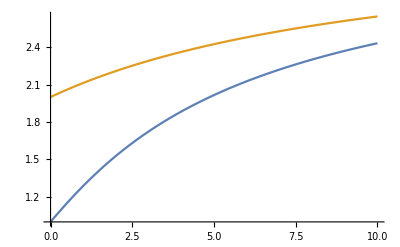

```mathematica
Plot[{ww1[t],ww2[t]},{t,0,10}]
```

```mathematica
(*Problem 2*)
(*Need a function with zeros at 0,1,2,3. For simplicity I will try a polynomial*)
(*It will need to have the form f(y)=Ky(y-1)(y-2)(y-3) *)
(*I will compute f'(y) to get info about steady states*)
Expand[D[y(y-1)(y-2)(y-3),y]]
```

-6+22 y-18 y^2+4 y^3

```mathematica
fPrime[y_]:=-6+22 y-18 y^2+4 y^3
```

```mathematica
{fPrime[0],fPrime[1],fPrime[2],fPrime[3]}
```

{-6,2,-2,6}

```mathematica
(*This shows that our properties are satisifed*)
(*More generally, it will hold for all K>0 so there is more than one system that is valid*)
```

```mathematica
(*Problem 3*)
```

```mathematica
Manipulate[Plot[{r*Log[y],y-1},{y,-10,10}],{r,-2,5}]
```

```mathematica
(*If y=1, the ln(y)=0 so the value of r is irrelevant*)
```

```mathematica
(*Part B*)
(*Equation is now y'=-r ln(u+1) + u*)

(*Problem 4*)
Manipulate[Plot[1+r*y+y^2,{y,-10,10}],{r,-5,5}]
```

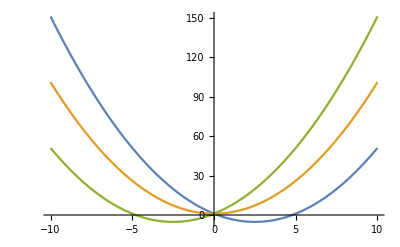

```mathematica
(*r=-5,0,5 Plot*)Plot[{1-5*y+y^2,1+y^2,1+5*y+y^2},{y,-10,10}]
```

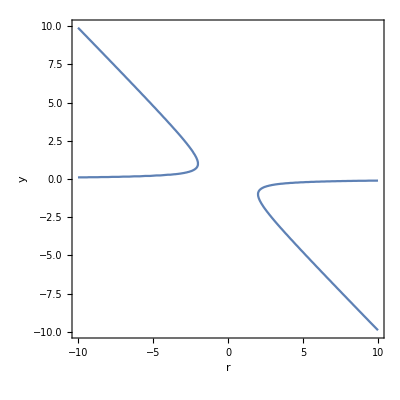

```mathematica
ContourPlot[1+r*y+y^2==0,{r,-10,10},{y,-10,10},AxesLabel->Automatic]
```

```mathematica
D[1+r*y+y^2,y]
```

r+2 y

```mathematica
(*TODO: PLOT WHICH PARTS OF ABOVE GRAPH ARE UNSTABLE/STABLE*)
```

```mathematica
(*Problem 5*)
Manipulate[Plot[y*(r-Exp[y]),{y,-1,1}],{r,-5,5}]
```

```mathematica
ff[r_]:=y*(r-Exp[y])
```

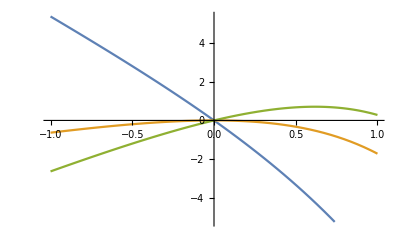

```mathematica
(*r=-5,0,5 Plot*)Plot[{ff[-5],ff[1],ff[3]},{y,-1,1}]
```

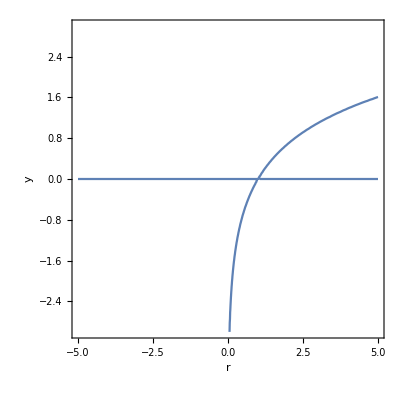

```mathematica
ContourPlot[y*(r-Exp[y])==0,{r,-5,5},{y,-3,3},AxesLabel->Automatic]
```

```mathematica
D[y*(r-Exp[y]),y]
```

-ⅇ^y+r-ⅇ^y y

```mathematica
(*TODO: PLOT WHICH PARTS OF ABOVE GRAPH ARE UNSTABLE/STABLE*)
```

```mathematica
(*Problem 6*)
Manipulate[Plot[y+r*y/(1+y^2),{y,-1,1}],{r,-5,15}]
```

```mathematica
ff[r_]:=y+r*y/(1+y^2)
```

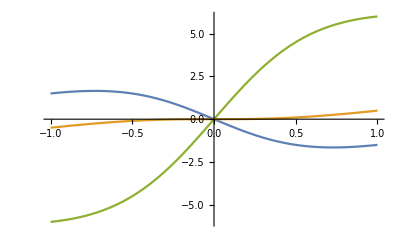

```mathematica
(*r=-5,0,5 Plot*)Plot[{ff[-5],ff[-1],ff[10]},{y,-1,1}]
```

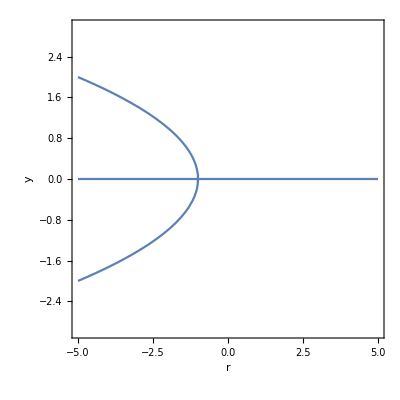

```mathematica
ContourPlot[y+r*y/(1+y^2)==0,{r,-5,5},{y,-3,3},AxesLabel->Automatic]
```

```mathematica
D[y+r*y/(1+y^2),y]
```

1-(2 r y^2)/((1+y^2)^2)+r/(1+y^2)